```mathematica
f[x_,y_]= Exp[x+y]
```

ⅇ^(x+y)

```mathematica
phiTri[a_,b_,c_,{x_,y_}]:=Module[{p,α,β},
{α,β}=LinearSolve[{{Norm[b-a]^2,(b-a).(c-a)},{(b-a).(c-a),Norm[c-a]^2}},{-1,-1}];
p = α (b-a) + β (c-a);
Return[1 + p.({x,y}-a)]
]
```

```mathematica
phiRef[x_,y_]={1-x-y,x,y}
```

{-x-y+1,x,y}

```mathematica
{aa, bb, cc}={{-1/4,1/8},{5/4,0},{1,4/3}}
```

(-1/4 | 1/8
5/4 | 0
1 | 4/3)

```mathematica
phiPhys[x_,y_]={phiTri[aa,bb,cc,{x,y}],phiTri[bb,cc,aa,{x,y}],phiTri[cc,aa,bb,{x,y}]}
```

{-128/189 (x+1/4)-8/63 (y-1/8)+1,116/189 (x-5/4)-(40 y)/63+1,(4 (x-1))/63+16/21 (y-4/3)+1}

```mathematica
{phiPhys[aa[[1]],aa[[2]]], phiPhys[bb[[1]],bb[[2]]],phiPhys[cc[[1]],cc[[2]]]}
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
R = Triangle[{{0,0},{1,0},{0,1}}]
```

Triangle[(0 | 0
1 | 0
0 | 1)]

```mathematica
T = Triangle[{aa,bb,cc}]
```

Triangle[(-1/4 | 1/8
5/4 | 0
1 | 4/3)]

```mathematica
fileNum = "9"
```

9

```mathematica
refQP = Import["/Users/katharine/Projects/PyPDE/Agnes/Quadrature/strang"<>fileNum <> "_x.txt", "Table"]
```

(0.873822 | 0.063089
0.063089 | 0.873822
0.063089 | 0.063089
0.501427 | 0.249287
0.249287 | 0.501427
0.249287 | 0.249287
0.636502 | 0.310352
0.636502 | 0.053145
0.310352 | 0.636502
0.310352 | 0.053145
0.053145 | 0.636502
0.053145 | 0.310352)

```mathematica
physQP = Table[aa + (bb -aa)p[[1]] + (cc-aa)p[[2]],{p,refQP}]
```

(1.13959 | 0.0920048
0.936911 | 1.17298
-0.0765052 | 0.193346
0.813748 | 0.363543
0.750713 | 0.69973
0.435539 | 0.395061
1.09269 | 0.420446
0.771185 | 0.109654
1.01116 | 0.855313
0.28196 | 0.150423
0.625346 | 0.887464
0.217658 | 0.493366)

```mathematica
w = Flatten[Import["/Users/katharine/Projects/PyPDE/Agnes/Quadrature/strang"<> fileNum <>"_w.txt", "Table"]]
```

{0.0508449,0.0508449,0.0508449,0.116786,0.116786,0.116786,0.0828511,0.0828511,0.0828511,0.0828511,0.0828511,0.0828511}

```mathematica
phiAtRefQP = Transpose[phiRef[refQP[[;;,1]],refQP[[;;,2]]]]
```

(0.063089 | 0.873822 | 0.063089
0.063089 | 0.063089 | 0.873822
0.873822 | 0.063089 | 0.063089
0.249287 | 0.501427 | 0.249287
0.249287 | 0.249287 | 0.501427
0.501427 | 0.249287 | 0.249287
0.053145 | 0.636502 | 0.310352
0.310352 | 0.636502 | 0.053145
0.053145 | 0.310352 | 0.636502
0.636502 | 0.310352 | 0.053145
0.310352 | 0.053145 | 0.636502
0.636502 | 0.053145 | 0.310352)

```mathematica
phiAtPhysQP = Transpose[phiPhys[physQP[[;;,1]],physQP[[;;,2]]]]
```

(0.063089 | 0.873822 | 0.063089
0.063089 | 0.063089 | 0.873822
0.873822 | 0.063089 | 0.063089
0.249287 | 0.501427 | 0.249287
0.249287 | 0.249287 | 0.501427
0.501427 | 0.249287 | 0.249287
0.053145 | 0.636502 | 0.310352
0.310352 | 0.636502 | 0.053145
0.053145 | 0.310352 | 0.636502
0.636502 | 0.310352 | 0.053145
0.310352 | 0.053145 | 0.636502
0.636502 | 0.053145 | 0.310352)

```mathematica
Qex=Integrate[f[x,y]phiPhys[x,y], {x, y}∈ T]//N
```

{0.842899,1.14667,1.53459}

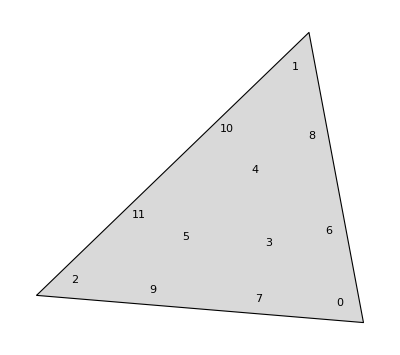

```mathematica
Graphics[{FaceForm[LightGray],EdgeForm[Black],T,Table[Text[i-1,physQP[[i]]],{i,1,Length[physQP]}]}]
```

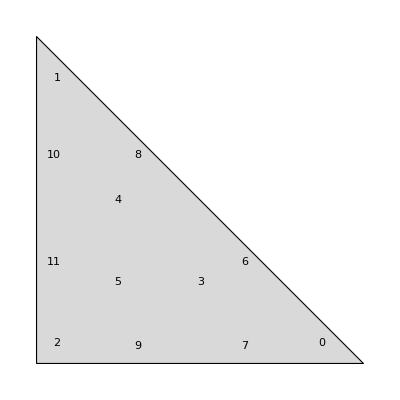

```mathematica
Graphics[{FaceForm[LightGray],EdgeForm[Black],R,Table[Text[i-1,refQP[[i]]],{i,1,Length[refQP]}]}]
```

```mathematica
fVals = f[physQP[[;;,1]],physQP[[;;,2]]]
```

{3.4267,8.24736,1.12394,3.24557,4.265,2.29469,4.54097,2.41292,6.46543,1.54092,4.53947,2.03608}

```mathematica
wf = w fVals
```

{0.17423,0.419336,0.0571467,0.379038,0.498094,0.267989,0.376224,0.199913,0.535668,0.127667,0.3761,0.168691}

```mathematica
wf phiAtRefQP
```

(0.010992 | 0.152246 | 0.010992
0.0264555 | 0.0264555 | 0.366425
0.049936 | 0.00360533 | 0.00360533
0.0944892 | 0.19006 | 0.0944892
0.124168 | 0.124168 | 0.249757
0.134377 | 0.066806 | 0.066806
0.0199945 | 0.239468 | 0.116762
0.0620436 | 0.127245 | 0.0106244
0.0284681 | 0.166246 | 0.340954
0.0812606 | 0.0396219 | 0.00678488
0.116723 | 0.0199878 | 0.239388
0.107372 | 0.00896509 | 0.0523537)

```mathematica
wf phiAtPhysQP
```

(0.010992 | 0.152246 | 0.010992
0.0264555 | 0.0264555 | 0.366425
0.049936 | 0.00360533 | 0.00360533
0.0944892 | 0.19006 | 0.0944892
0.124168 | 0.124168 | 0.249757
0.134377 | 0.066806 | 0.066806
0.0199945 | 0.239468 | 0.116762
0.0620436 | 0.127245 | 0.0106244
0.0284681 | 0.166246 | 0.340954
0.0812606 | 0.0396219 | 0.00678488
0.116723 | 0.0199878 | 0.239388
0.107372 | 0.00896509 | 0.0523537)

```mathematica
Chop[Norm[wf (phiAtPhysQP - phiAtRefQP)]]
```

0

```mathematica
Qref = Total[wf phiAtRefQP]Area[T]
```

{0.842901,1.14667,1.53458}

```mathematica
Qphys =Total[wf phiAtPhysQP] Area[T]
```

{0.842901,1.14667,1.53458}

```mathematica
Qex
```

{0.842899,1.14667,1.53459}

```mathematica
FortranForm[Qex]
```

List(0.842898747945908,1.1466748135442901,
     -  1.5345857052411658)

### Results

```mathematica
errs = {0.25974, 0.012262, 0.0078317, 0.00027245, 0.00014704, 1.2301 10^-6}
```

{0.25974,0.012262,0.0078317,0.00027245,0.00014704,1.2301×10^-6}

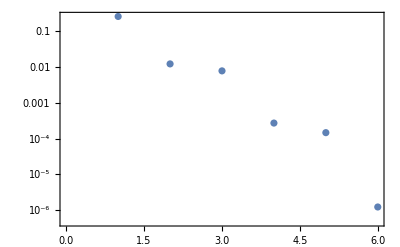

```mathematica
ListLogPlot[errs]
```

```mathematica
data = Transpose[{Table[i,{i,1,Length[errs]}],Log[errs]}]
```

(1 | -1.34807
2 | -4.40125
3 | -4.84958
4 | -8.20806
5 | -8.82481
6 | -13.6084)

```mathematica
fit[p_]=Exp[Fit[data,{1,p},p]]
```

ⅇ^(0.919722-2.2266 p)

```mathematica
fit[0]
```

2.50859

```mathematica
g[p_]=Exp[2]fit[p]
```

ⅇ^(2.91972-2.2266 p)

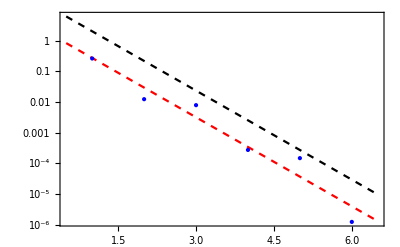

```mathematica
Show[
LogPlot[{fit[p],g[p]},{p,0.5,6.5},PlotStyle->{Directive[Dashed,Red],Directive[Dashed,Black]},PlotRange->All],
ListLogPlot[errs,PlotStyle->Directive[Blue, PointSize[Large]]]
]
```